## Bosted Fit

```mathematica
z=Sqrt[Q2]
GEbosted= 1/(1+0.62*z+0.68*z^2+2.80*z^3+0.83*z^4)
GMbosted=2.7972*(1/(1+0.35*z+2.44*z^2+0.50*z^3+1.04*z^4+0.34*z^5))
Rffbosted=2.7972*GEbosted/GMbosted
RffPT=1-0.12*Q2
```

√Q2

1/(1+0.62 √Q2+0.68 Q2+2.8 Q2^(3/2)+0.83 Q2^2)

2.7972/(1+0.35 √Q2+2.44 Q2+0.5 Q2^(3/2)+1.04 Q2^2+0.34 Q2^(5/2))

(1. (1+0.35 √Q2+2.44 Q2+0.5 Q2^(3/2)+1.04 Q2^2+0.34 Q2^(5/2)))/(1+0.62 √Q2+0.68 Q2+2.8 Q2^(3/2)+0.83 Q2^2)

1-0.12 Q2

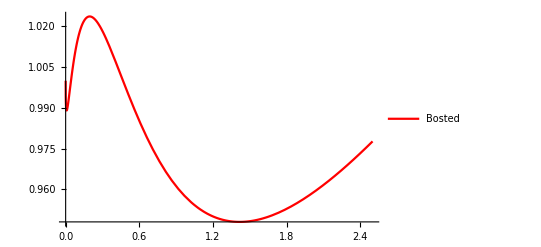

```mathematica
P1=Plot[Rffbosted,{Q2,0,2.5},PlotStyle->Red,PlotLegends-> Placed[LineLegend[{"Bosted"}],{0.2,0.5}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14]]
```

## Arrington Fit

```mathematica
x=Q2
GEarr=1/(1+3.226*x+1.508*x^2-0.3773*x^3+0.611*x^4-0.185*x^5)
GMarr=2.7972*(1/(1+3.19*x+1.355*x^2+0.151*x^3-1.14*10^-2*x^4+5.33*10^-4x^5-9*10^-6x^6))
Rffarrington= 2.7972*GEarr/GMarr
```

Q2

1/(1+3.226 Q2+1.508 Q2^2-0.3773 Q2^3+0.611 Q2^4-0.185 Q2^5)

2.7972/(1+3.19 Q2+1.355 Q2^2+0.151 Q2^3-0.0114 Q2^4+0.000533 Q2^5-(9 Q2^6)/1000000)

(1. (1+3.19 Q2+1.355 Q2^2+0.151 Q2^3-0.0114 Q2^4+0.000533 Q2^5-(9 Q2^6)/1000000))/(1+3.226 Q2+1.508 Q2^2-0.3773 Q2^3+0.611 Q2^4-0.185 Q2^5)

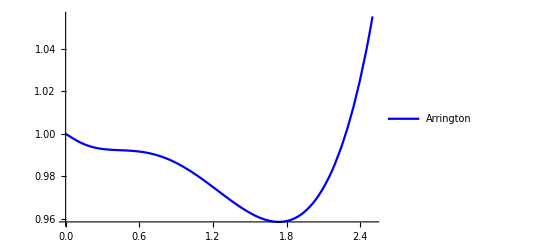

```mathematica
P2=Plot[Rffarrington,{Q2,0,2.5},PlotStyle->Blue,PlotLegends-> Placed[LineLegend[{"Arrington"}],{0.2,0.4}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14]]
```

## PT data Linear fit

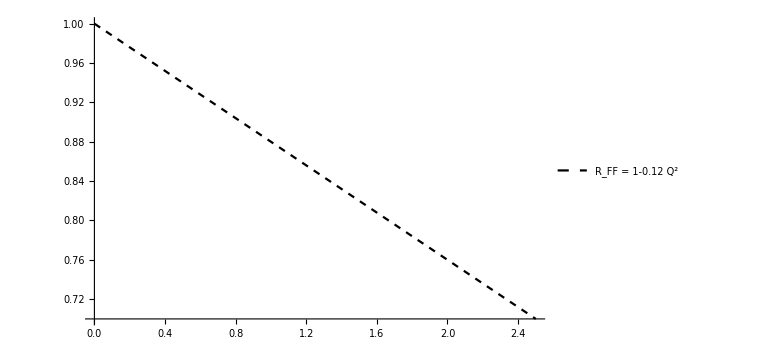

```mathematica
P3=Plot[1-0.12*Q2,{Q2,0,2.5},PlotStyle->{Black,Dashed}, PlotLegends-> Placed[LineLegend[{"R_FF = 1-0.12 Q^2"}],{0.2,0.3}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->16]]
```

## (Pade)

```mathematica
a1=3.439
a2=-1.602
a3=0.068
b1=15.055
b2=48.061
b3=99.304
b4=0.012
b5=8.650
c1=-1.465
c2=1.260
c3=0.262
d1=9.627
d2=0.000
d3=0.000
d4=11.179
d5=13.245
GEpade= (1+a1*tau+a2*tau^2+a3*tau^3)/(1+b1*tau+b2*tau^2+b3*tau^3+b4*tau^4+b5*tau^5)
GMpade= 2.7972*((1+c1*tau+c2*tau^2+c3*tau^3)/(1+d1*tau+d2*tau^2+d3*tau^3+d4*tau^4+d5*tau^5))
tau=Q2/(4*0.938^2)
RffBern= 2.7972*GEpade/GMpade
```

3.439

-1.602

0.068

15.055

48.061

99.304

0.012

8.65

-1.465

1.26

0.262

9.627

0.

0.

11.179

13.245

(1+3.439 tau-1.602 tau^2+0.068 tau^3)/(1+15.055 tau+48.061 tau^2+99.304 tau^3+0.012 tau^4+8.65 tau^5)

(2.7972 (1-1.465 tau+1.26 tau^2+0.262 tau^3))/(1.+9.627 tau+11.179 tau^4+13.245 tau^5)

0.284141 Q2

(1. (1+0.977162 Q2-0.129339 Q2^2+0.00155995 Q2^3) (1.+2.73543 Q2+0.0728686 Q2^4+0.0245315 Q2^5))/((1-0.416267 Q2+0.101728 Q2^2+0.00601041 Q2^3) (1+4.27775 Q2+3.88027 Q2^2+2.27808 Q2^3+0.0000782201 Q2^4+0.0160209 Q2^5))

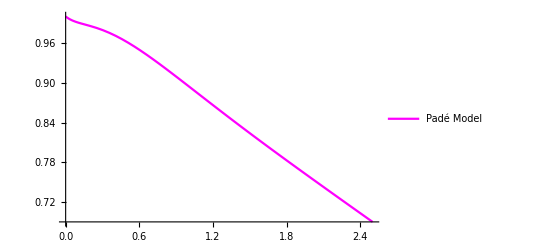

```mathematica
P4=Plot[RffBern,{Q2,0,2.5},PlotStyle->Magenta,PlotLegends-> Placed[LineLegend[{"Padé Model"}],{0.2,0.2}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14]]
```

## Dipole

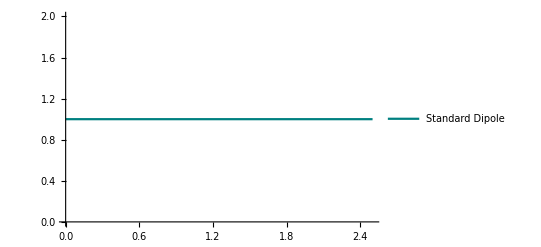

```mathematica
P5=Plot[1,{Q2,0,2.5},PlotStyle->{Blend[{Green,Blue}]},PlotLegends-> Placed[LineLegend[{"Standard Dipole"}],{0.2,0.1}],LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14]]
```

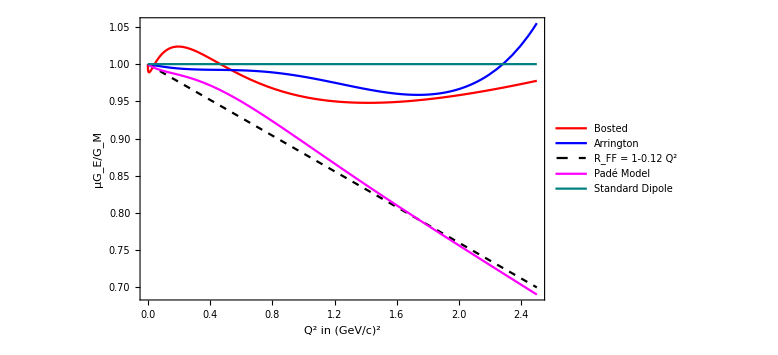

```mathematica
Show[P1,P2,P3,P4,P5,PlotRange->All,Frame-> True,FrameTicks->All,FrameLabel->{Style["Q^2 in (GeV/c)^2",Bold,18,Black],Style["μG_E/G_M",Bold,18,Black]},Axes-> False,  ImageSize-> Large,FrameTicksStyle-> Directive[Black,14]]
```